```mathematica
m1={{1, 0, 0}, {0, Sqrt[1/3], Sqrt[2/3]}, {0, -Sqrt[2/3], Sqrt[1/3]}}
```

{{1,0,0},{0,1/(√3),√(2/3)},{0,-√(2/3),1/(√3)}}

```mathematica
m2={{Sqrt[1/2], Sqrt[1/2], 0}, {-Sqrt[1/2], Sqrt[1/2], 0}, {0, 0, 1}}
```

{{1/(√2),1/(√2),0},{-1/(√2),1/(√2),0},{0,0,1}}

```mathematica
(m=m2.m1)//MatrixForm
```

(1/(√2) | 1/(√6) | 1/(√3)
-1/(√2) | 1/(√6) | 1/(√3)
0 | -√(2/3) | 1/(√3))

```mathematica
(mm=Transpose[m])//MatrixForm
```

(1/(√2) | -1/(√2) | 0
1/(√6) | 1/(√6) | -√(2/3)
1/(√3) | 1/(√3) | 1/(√3))

```mathematica
mm.{x,y,z}
```

{x/(√2)-y/(√2),x/(√6)+y/(√6)-√(2/3) z,x/(√3)+y/(√3)+z/(√3)}

```mathematica
MapThread[#1->#2&,{{xx,yy,zz},mm.{x,y,z}}]
```

{xx→x/(√2)-y/(√2),yy→x/(√6)+y/(√6)-√(2/3) z,zz→x/(√3)+y/(√3)+z/(√3)}

```mathematica
-a zz+xx^2+yy^2/.MapThread[#1->#2&,{{xx,yy,zz},mm.{x,y,z}}]//Simplify
```

1/3 (-√3 a (x+y+z)+2 (x^2+y^2-y z+z^2-x (y+z)))

```mathematica
a mm[[1]]Cos[α]z+a mm[[2]]Sin[α]z+mm[[3]]z+1/3{1,1,1}/.{α->Pi/2,a->-1/(√2),z->-2/(√3)}
```

{0,0,-1}

```mathematica
{b12,b23,b31}=a mm[[1]]Cos[α]z+a mm[[2]]Sin[α]z+mm[[3]]z+1/3{1,1,1}/.{a->-1/(√2)}//Simplify
```

{1/6 (2+2 √3 z-3 z Cos[α]-√3 z Sin[α]),1/6 (2+2 √3 z+3 z Cos[α]-√3 z Sin[α]),1/3 (1+√3 z+√3 z Sin[α])}

```mathematica
denum=(1+3(b12^2+b23^2+b31^2)//Simplify)
```

2+2 √3 z+(9 z^2)/2

```mathematica
numx=(2(b12-b12^2+b23 b31)//Simplify);
numy=(2(b23-b23^2+b31 b12)//Simplify);
numz=(2(b31-b31^2+b12 b23)//Simplify);
```

```mathematica
numx
```

2/3+(2 z)/(√3)-z^2/2+√3 z^2 Cos[α]+z^2 Sin[α]

```mathematica
numy//Expand
```

2/3+(2 z)/(√3)-z^2/2-√3 z^2 Cos[α]+z^2 Sin[α]

```mathematica
numz//Expand
```

2/3+(2 z)/(√3)-z^2/2-2 z^2 Sin[α]

```mathematica
p1=ParametricPlot3D[{numx,numy,numz}/denum,{z,-1.3,0},{α,0,2Pi}];
p2=ParametricPlot3D[{0,0,x},{x,-1,1}];
Show[p1,p2,PlotRange->All]
```

-Graphics3D-

```mathematica
Solve[{1/3+z/(√3)+(a z)/(√6),1/3+z/(√3)+(a z)/(√6),1/3+z/(√3)-√(2/3) a z}=={0,0,-1},{a,z}]
```

{{a→-1/(√2),z→-2/(√3)}}

```mathematica
p1=ParametricPlot3D[{a mm[[1]]Cos[α]z+a mm[[2]]Sin[α]z+mm[[3]]z+1/3{1,1,1}/.a->-1/Sqrt[2]},{z,-2,2},{α,0+Pi/2,0.1+Pi/2}];
p2=Plot3D[1/3,{x,-1,1},{y,-1,1}];
p3=Plot3D[-1,{x,-1,1},{y,-1,1}];
Show[p1,p3,PlotRange->All]
```

-Graphics3D-

```mathematica
Solve[0==2(bt(1-3bs))/(1+9bs^2+6bt^2),bt]
```

{{bt→0}}

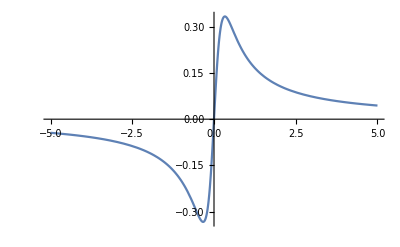

```mathematica
Plot[2bs/(1+9bs^2),{bs,-5,5}]
```